```mathematica
f[x_,y_]=Subscript[r, 1] x(1-x/Subscript[k, 1])-Subscript[α, 1] x y;
g[x_,y_]=Subscript[r, 2] y(1-y/Subscript[k, 2])-Subscript[α, 2] x y;
w[x_,y_]=Subscript[r, 1] x(1-x/Subscript[k, 1])-Subscript[α, 1] x y+Subscript[r, 2] y(1-y/Subscript[k, 2])-Subscript[α, 2] x y;
```

```mathematica
{Subscript[r, 1],Subscript[r, 2]}={0.05,0.08};
{Subscript[k, 1],Subscript[k, 2]}={1.5 10^5, 4 10^5};
{Subscript[α, 1],Subscript[α, 2]}={10^-8,10^-8};
```

```mathematica
{xsol, ysol} = {0.6910 10^5, 1.9654 10^5};
w[xsol, ysol]
```

9589.38

```mathematica
Solve[Grad[w[x,y],{x,y}]=={0,0},{x,y}]
```

{{x→69103.7,y→196545.}}

```mathematica
Plot3D[w[x,y],{x,-300000,300000},{y,-300000,300000}]
```

-Graphics3D-

```mathematica
NSolve[w[x,y]==0,{x,y}]
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with 151145\ x/110742 - 17791\ y/18457 == 1.

{{x→214096.,y→303144.},{x→0.508315,y→-0.317696}}

```mathematica
NSolve[f[x,y]==0,{x,y}]
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -17791\ x/18457 + 151145\ y/110742 == 1.

{{x→146888.,y→103740.},{x→0.,y→0.732687}}

```mathematica
Plot3D[f[x,y],{x,-300000,300000},{y,-300000,300000}]
```

-Graphics3D-

```mathematica
inequal1[x_,y_]=((Subscript[r, 1]-Subscript[α, 1] y)Subscript[k, 1])/Subscript[r, 1]-x;
inequal2[x_,y_]=((Subscript[r, 2]-Subscript[α, 2] x)Subscript[k, 2])/Subscript[r, 2]-y;
```

```mathematica
RegionPlot3D[inequal1[x,y] ≥ 0 &&inequal2[x,y]≥0,{x,-300000,300000},{y,-300000,300000}]
```

RegionPlot3D::pllim: Range specification Lighting → Automatic is not of the form {x, xmin, xmax}.

General::stop: Further output of RegionPlot3D :: pllim will be suppressed during this calculation.

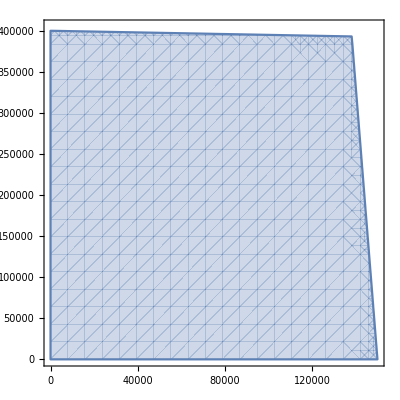

```mathematica
RegionPlot[inequal1[x,y]≥0&&inequal2[x,y]≥0,{x,0,150000},{y,0,405000}]
```

```mathematica
Reduce[inequal1[x,y]≥0&&inequal2[x,y]≥0&&x>0&&y>0,{x,y}]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

(0<x≤138207.&&0<y≤0.05 (8.×10^6-1. x))||(138207.<x<150000.&&0<y≤0.333333 (1.5×10^7-100. x))

```mathematica
-x+3.*^6 (0.05-y/100000000)
```